# The distribution of amino acid changes in different species

One sentence description of topic.

Zhamilya Bilyalova, Jun. 24,  2018

Write a 3-5 sentence basic introduction of the topic, particularly why it’s interesting. Note that the title should be as straightforward as possible (Rhythmic Timelines, not: Sonifying Clave son – Exploring Musical Rhythm), so the introduction provides the opportunity to elaborate and engage the reader. Don’t make the subjects overly general—have them match the specificity of the content.

RNA editing is a process that changes a RNA transcript such that it would no longer correspond to a sequence of DNA in a genome. A-to-I RNA editing is widespread in animals and results in the modification of a adenosine to inosine which will be read as a guanine. A-to-I editing in messenger RNA (mRNA) can cause changes in the amino acid sequence of a protein (amino acid recoding). It was recently discovered that RNA editing and amino acid changes are widespread in cephalopods (octopus and squid). Article: Trade-off between Transcriptome Plasticity and Genome Evolution in Cephalopods, Cell 169, 191–202 (2017).

	(RNA is a copy of one specific part of DNA, but after being created it can still be changed in a way that the DNA did not program it. There can be many types of changes. We are looking at the one where nucleotide A changes to nucleotide G, which changes the codon. Codons (64 combinations in total) are codes for specific amino acids. (one amino acids can relate to more than one codon). Nucleotides are being changed by enzymes that catalyze the editing.)

Codons:          -Graphics-

Amino acids:

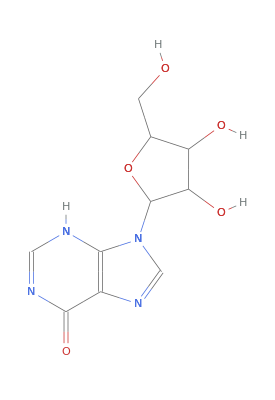
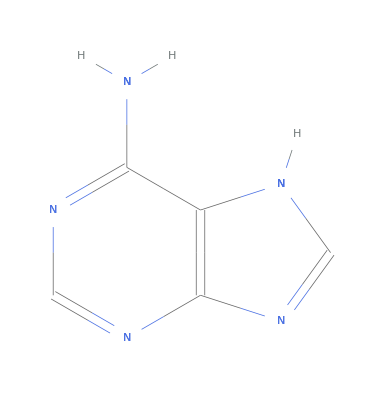
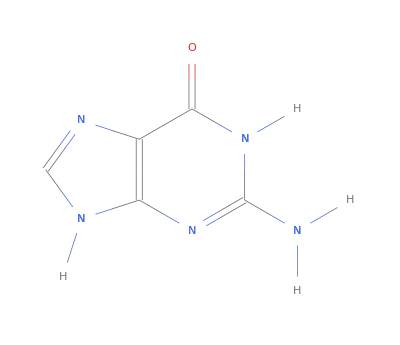
-Graphics-Inosine | -Graphics-Adenine | -Graphics-Guanine

```mathematica
Grid[ {
 Map[Labeled[ChemicalData[#],#,Left]&,{"Inosine","Adenine","Guanine"}]
}
,Spacings->2]
```

## Section Header

set up assumptions and provide definitions.

Description of the data:
	The data set consists of calculated expected distribution (“Expected amount”, “Expected frequency”) and observed distribution (“edits”, “frequency”) of amino acid changes in humans, four cephalopod species, and conserved edits from those species.
KR  represents a change from amino acid K to amino acid R. syn means synonymous, without any changes to amino acid, likely doesn’t have an effect. stop_W means stop to w, causes a significant change in a protein sequence.

All types of amino acids are categorized as either radical or conserved. Radical changes are those that change the physicochemical property of the amino acid while conservative changes do not. The ratio of radical to conservative changes indicates how many changes are likely to have a negative effect

-Graphics-
	Amino acid changes also can be random or non-random: - Random edits = likely to be slightly bad = doesn't make an animal better - Non-random edits = likely to be good = likely to be actively preserved in the population = seen more in conserved.
	In humans most changes are random, therefore, they are most likely to have a negative effect. In Individual cephalopod species, amino acid changes are a lot less random and they are less likely to have a negative effect. In conserved, changes are least random (assumption) and most likely to have a positive effect. 1. Human vs. individual ocean species 2. Individual cephalopod species vs. conserved

```mathematica
Code (* demonstrate a general case*)
```

Another way to start an exposition, or to expand on the basics, is to provide an example showing the application of the topic. The example might be something you arrive at by the end of the exposition, repeating that conclusion here is acceptable if it's reasonably self-contained. It might also be an example a problem scenario and the exposition explains a solution.

## Data

```mathematica
SetDirectory["/Users/jamilya_bilyalova/Documents/DS_CLASS_2017-18_Zhamilya/class_project/Data"] ;
```

```mathematica
data=SemanticImport["editingcodonsimplifieddata.xlsx"](* Importing Excel document with data *)
```

Dataset[<>]

## Visualisation and Exploration

#### Expected frequency vs. actual frequency

```mathematica
legend=Association@With[{list=Normal[datagrouped[["human",All,"Change"]]]},
Thread[list->RandomColor[Length@list]]
]
```

<|KR→RGBColor[0.786030300234128, 0.6570196400712873, 0.28693486244729116],SG→RGBColor[0.5376515584745132, 0.058290262418320804, 0.31349325225004043],IM→RGBColor[0.7408414497743829, 0.5153478375608862, 0.6596887862203475],TA→RGBColor[0.901675170056256, 0.15683343021140383, 0.2752880589272917],IV→RGBColor[0.2162372302360358, 0.520529299330726, 0.9484453590451989],MV→RGBColor[0.5598724341254826, 0.8417293621682949, 0.5573428009270127],HR→RGBColor[0.4576073110894203, 0.29319214795741133, 0.4619326695636268],NS→RGBColor[0.4830889616970211, 0.5840000261734266, 0.6195038946239142],ND→RGBColor[0.9360817810961088, 0.5940792655852174, 0.6094984271714585],QR→RGBColor[0.6215639628286491, 0.5697155068182203, 0.40185510387388246],KE→RGBColor[0.8216213612635028, 0.7839688363914232, 0.26416711771638024],EG→RGBColor[0.2726930331120625, 0.7116625573096229, 0.2991866981933311],RG→RGBColor[0.15885604882803328, 0.05349527062649195, 0.897482859539414],YC→RGBColor[0.6246820028617561, 0.2982952013064857, 0.547236857360051],DG→RGBColor[0.8091737324588757, 0.8221634083997655, 0.6757396690118387],stop-W→RGBColor[0.8822190452753051, 0.7209781638558457, 0.5805568500819969]|>

```mathematica
Normal[datagrouped[["human",All,{"Expected_frequency","Frequency","Change"}]]][[1]]
{legend[#Change],Point[{#["Expected_frequency"],#["Frequency"]}]}&@%
```

<|Expected_frequency→0.0606061,Frequency→0.142487,Change→KR|>

{RGBColor[0.786030300234128, 0.6570196400712873, 0.28693486244729116],Point[{0.0606061,0.142487}]}

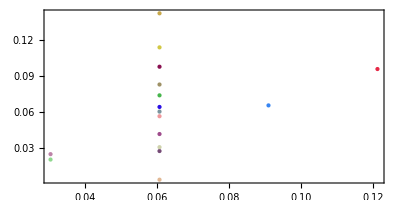

```mathematica
Normal[datagrouped[["human",All,{"Expected_frequency","Frequency","Change"}]]];
Graphics[Flatten[{legend[#Change],Point[{#["Expected_frequency"],#["Frequency"]}]}&/@%],Frame->True,AspectRatio->1/2]
```

```mathematica
?Legended
```

Legended[expr,leg] displays expr with legend leg. 
Legended[expr,lbl] indicates in plotting and charting functions that a legend entry for expr should be created, with label lbl.

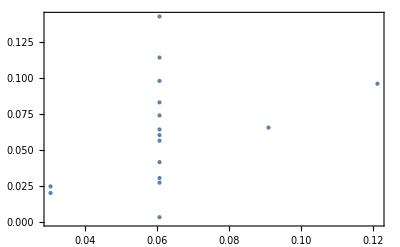

```mathematica
ListPlot[datagrouped[["human",All,{"Expected_frequency","Frequency"}]],PlotStyle->PointSize[Medium],Frame->True]
```

```mathematica
?PlotLabels
```

PlotLabels is an option for visualization functions that specifies what labels to use for each data source.

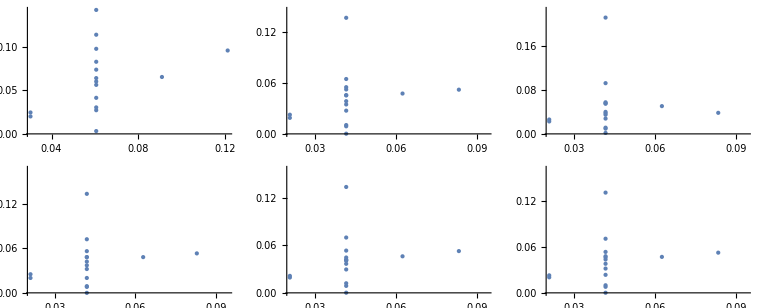

```mathematica
GraphicsGrid@Partition[Table[ListPlot[datagrouped[[key,All,{"Expected_frequency","Frequency"}]],PlotStyle->PointSize[Medium]],{key,Normal@Keys@datagrouped}],3]
```

```mathematica
Show[bp,Frame->True,FrameLabel->{{"left label","right label"},{"bottom label","top label"}}]
```

ggplot(data = df) +
  geom_point(mapping = aes(x = Expected_frequency, y = frequency, color = Change)) +
  facet_wrap(~sp_name, ncol=3) +
  coord_fixed() +
  ggtitle(“Expected frequency vs. actual frequency”)

```mathematica
aList={{1,1},{2,3},{4,5},{6,7}};
colorList={Black,Red,Blue,Yellow};
bList={#}&/@aList;
ListPlot[bList,PlotStyle->colorList]
```

```mathematica
LineLegend[ColorData[97]/@{1,2,3},{Sin[x],Cos[y],Tan[z]}]
```

```mathematica
WebImageSearch["colorful birds"]
WebImageSearch["colorful birds","Thumbnails"]
```

```mathematica
Show[bp,Frame->True,FrameLabel->{{"left label","right label"},{"bottom label","top label"}}]
```

```mathematica
,PlotLegends -> data[[All,"Change"]],
PlotStyle->PointSize[Medium],AxesLabel->Automatic
color=change,PlotLegends->{0.3,0.5,0.8} PlotTheme->"Scientific"
```

Expected frequency vs. actual frequency

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins

derivation

applications

common misunderstandings

recent developments

unanswered questions

## Further explorations

Name of a related topic for exploration

Name of another related topic for exploration (repeat as needed)

## Author contact information

emailaddress@author.com

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)